# Initialization Values

```mathematica
storm="floyd_norivers";

If[storm=="floyd"∨storm=="floyd_noriver",
rundays=6;
];
If[storm=="irene",
rundays=10;
];
If[storm=="isabel",
rundays=5.5;
];

runseconds=rundays*24*60*60;



results=ts72[StringJoin["D:\\Dropbox\\",storm,"\\hurricane\\fort.72"]];
basedirectory=StringJoin["D:\\Dropbox\\",storm];
uxs=results[[1]];
vys=results[[2]];
nstations=results[[3]];
timestamps=results[[4]];
originVector={0,1};(* grid direction of true north*)
timestampseconds=1.0; (*seconds per unit of timestamp. i.e. ADCIRC outputs timestamps in seconds, so 1.*)
timestamps=timestamps*timestampseconds;

(*enter simulation start time here. Is used later on to orient NBDC data*)
If[storm=="irene",
yystart=2011;
MMstart=07;
DDstart=06;
];

If[storm=="floyd"∨storm=="floyd_norivers",
yystart=1999;
MMstart=08;
DDstart=11;
hhstart=00;
mmstart=00;
];

If[storm=="isabel",
yystart=2003;
MMstart=07;
DDstart=31;
hhstart=00;
mmstart=00;
];

simstartdate={yystart,MMstart,DDstart,hhstart,mmstart,0};
simstartseconds=AbsoluteTime[simstartdate];
```

# Convert To NBDC Standard Format

anglesAndMagsClockwiseFromNorth[us_,vs_]:={angles,magnitudes}

```mathematica
temp=Table[anglesAndMagsClockwiseFromNorth[-uxs[[i]],-vys[[i]]],{i,1,nstations}];
windstrength=Table[temp[[i,2]],{i,1,nstations}];
clockwiseAngleDeg=Table[temp[[i,1]],{i,1,nstations}];
Clear[temp];
```

# Read In NBDC File

```mathematica
If[storm=="irene",
(*NBDC_41001, NDBC_41002, NBDC41025, NBDC_CLKN7, NBDC_DUKN7, NBDC_FPSN7*)

stnfilelist={"D:\\Dropbox\\irene\\observed winds\\NBDC_41001.txt",
"NA",
"NA",
"D:\\Dropbox\\irene\\observed winds\\NBDC_CLKN7.txt",
"D:\\Dropbox\\irene\\observed winds\\NBDC_DUKN7.txt",
"D:\\Dropbox\\irene\\observed winds\\NBDC_41013 FPSN7 standin.txt"};
stnnames={"41001","na","NA","CLKN7","DUKN7","41013"};
sitenumbers={1,4,5,6};
];

If[storm=="floyd"∨storm=="floyd_norivers",
stnfilelist={"D:\\Dropbox\\floyd\\observed winds\\ndbc 41001.txt",
"D:\\Dropbox\\floyd\\observed winds\\ndbc 41002.txt",
"NA",
"D:\\Dropbox\\floyd\\observed winds\\ndbc clkn7.txt",
"NA",
"D:\\Dropbox\\floyd\\observed winds\\ndbc fpsn7.txt"};
stnnames={"41001","41002","NA","CLKN7","na","FPSN7"};
sitenumbers={1,2,4,6};
];

If[storm=="isabel",
stnfilelist={"D:\\Dropbox\\Isabel\\observed winds\\ndbc_41001.txt",
"D:\\Dropbox\\Isabel\\observed winds\\ndbc_41002.txt",
"D:\\Dropbox\\Isabel\\observed winds\\ndbc_41025.txt",
"D:\\Dropbox\\Isabel\\observed winds\\ndbc_clkn7.txt",
"NA",
"D:\\Dropbox\\Isabel\\observed winds\\ndbc_fpsn7.txt"};
stnnames={"41001","41002","41025","CLKN7","na","FPSN7"};
sitenumbers={1,2,3,4,6};
];






secondsSinceSimStart=Table[0,{Length[sitenumbers]}];
datestart=secondsSinceSimStart;
secstart=datestart;
secend=datestart;
WDIR=datestart;
WSPD=datestart;

Do[
sitenumber=sitenumbers[[j]];
stnpath=stnfilelist[[sitenumber]];

(*for irene, 41002 is not available*)
If[storm=="irene",
ncols=18];
If[storm=="floyd"∨storm=="floyd_norivers",
ncols=16];
If[storm=="isabel",
ncols=17];

If[storm=="irene",
yy=ReadNBDCfile[stnpath,2,ncols,1,Number];
MM=ReadNBDCfile[stnpath,2,ncols,2,Number];
DD=ReadNBDCfile[stnpath,2,ncols,3,Number];
hh=ReadNBDCfile[stnpath,2,ncols,4,Number];
mm=ReadNBDCfile[stnpath,2,ncols,5,Number];
WDIR[[j]]=ReadNBDCfile[stnpath,2,ncols,6,Number];
WSPD[[j]]=ReadNBDCfile[stnpath,2,ncols,7,Number];
];

If[storm=="floyd"∨storm=="floyd_norivers",
yy=ReadNBDCfile[stnpath,2,ncols,1,Number];
MM=ReadNBDCfile[stnpath,2,ncols,2,Number];
DD=ReadNBDCfile[stnpath,2,ncols,3,Number];
hh=ReadNBDCfile[stnpath,2,ncols,4,Number];
mm=Table[0,{Length[hh]}];
WDIR[[j]]=ReadNBDCfile[stnpath,2,ncols,5,Number];
WSPD[[j]]=ReadNBDCfile[stnpath,2,ncols,6,Number];
];

If[storm=="isabel",
yy=ReadNBDCfile[stnpath,1,ncols,1,Number];
MM=ReadNBDCfile[stnpath,1,ncols,2,Number];
DD=ReadNBDCfile[stnpath,1,ncols,3,Number];
hh=ReadNBDCfile[stnpath,1,ncols,4,Number];
mm=Table[0,{Length[hh]}];
WDIR[[j]]=ReadNBDCfile[stnpath,1,ncols,5,Number];
WSPD[[j]]=ReadNBDCfile[stnpath,1,ncols,6,Number];
];



Do[
If[WDIR[[j,k]]>360,WDIR[[j,k]]=0];
If[WSPD[[j,k]]==99,WSPD[[j,k]]=-1];
,{k,1,Length[WDIR[[j]]]}];
l2=Length[yy];
datestart[[j]]={yy[[1]],MM[[1]],DD[[1]],hh[[11]],mm[[1]],0};
secondsSinceSimStart[[j]]=Table[AbsoluteTime[{yy[[i]],MM[[i]],DD[[i]],hh[[i]],mm[[i]],0}]-AbsoluteTime[simstartdate],{i,1,l2}];
secstart[[j]]=secondsSinceSimStart[[j]][[1]];
secend[[j]]=secondsSinceSimStart[[j]][[l2]];
,{j,1,Length[sitenumbers]}];
```

# Plot forecast vs. observed

Create Observed Time/Ob Scatters

```mathematica
(*select observed entries to plot - filter out all observations occurring before simulation start, or after simulation end*)
WDIRobscatter=Table[0,{Length[sitenumbers]}];
WSPDobscatter=WDIRobscatter;

Do[

inctable={};
Do[
If[secondsSinceSimStart[[j,i]]>timestamps[[1]],
If[secondsSinceSimStart[[j,i]]<timestamps[[Length[timestamps]]],
inctable=Flatten[Append[inctable,{secondsSinceSimStart[[j,i]]-timestamps[[1]]+simstartseconds,WDIR[[j,i]]}]];
]
]
,{i,1,Length[secondsSinceSimStart[[j]]]}];
WDIRobscatter[[j]]=Partition[inctable,2];




inctable={};
Do[
If[secondsSinceSimStart[[j,i]]>timestamps[[1]],
If[secondsSinceSimStart[[j,i]]<timestamps[[Length[timestamps]]],
inctable=Flatten[Append[inctable,{(secondsSinceSimStart[[j,i]]-timestamps[[1]])+simstartseconds,WSPD[[j,i]]}]];
]
]
,{i,1,Length[secondsSinceSimStart[[j]]]}];
WSPDobscatter[[j]]=Partition[inctable,2];

,{j,1,Length[sitenumbers]}];
```

Create Simulation Scatters

```mathematica
WSPDsimscatters=Table[0,{i,1,nstations}];
WDIRsimscatters=Table[0,{i,1,nstations}];

Do[
WSPDsimscatters[[i]]=Transpose[Table[{timestamps-timestamps[[1]]+simstartseconds,windstrength[[i]]}]];
WDIRsimscatters[[i]]=Transpose[Table[{timestamps-timestamps[[1]]+simstartseconds,clockwiseAngleDeg[[i]]}]];
,{i,1,nstations}];

WSPDsimscatters=Delete[WSPDsimscatters,Position[stnfilelist,"NA"]];
WDIRsimscatters=Delete[WDIRsimscatters,Position[stnfilelist,"NA"]];
stnnamestrue=Delete[stnnames,Position[stnfilelist,"NA"]];
```

```mathematica
Transpose[WSPDsimscatters[[1]]][[1]]//Max//DateString
```

Mon 16 Aug 1999 22:00:00

Plot Grid of Observed/Actual

```mathematica
simendseconds=simstartseconds+runseconds




plotlist=Table[
{
Show[
	scatterplot[
		WSPDobscatter[[sitenumber]],
		simstartseconds,
		simendseconds,
		-1,
		Max[{Max[Transpose[WSPDobscatter[[sitenumber]]][[2]]]*1.3,Max[Transpose[WSPDsimscatters[[sitenumber]]][[2]]]*1.3}],
		"\nm/s",
		"Date",
		StringJoin["\nNBDC ",stnnamestrue[[sitenumber]]," Wind Speeds"],
		1,
		False,
		Black]
,
	scatterplot[
		WSPDsimscatters[[sitenumber]],
		simstartseconds,
		simendseconds,
		-1,
		Max[{Max[Transpose[WSPDobscatter[[sitenumber]]][[2]]]*1.3,Max[Transpose[WSPDsimscatters[[sitenumber]]][[2]]]*1.3}],
		"\nm/s",
		"Date",
		StringJoin["\nNBDC ",stnnamestrue[[sitenumber]]," Wind Speeds"],
		1,
		True,
		Blue]


	,
	ImageSize->Large],
Show[

	scatterplot[
		WDIRsimscatters[[sitenumber]],
		simstartseconds,
		simendseconds,
		-20,
		380,
		"\nDegrees From North (Clockwise)",
		"Date",
		StringJoin["\nNBDC ",stnnamestrue[[sitenumber]]," Wind Direction"],
		1,
		True,
		Blue]
,
	scatterplot[
		WDIRobscatter[[sitenumber]],
		simstartseconds,
		simendseconds,
		-20,
		380,
		"\nDegrees From North (Clockwise)",
		"Date",
		StringJoin["\nNBDC ",stnnamestrue[[sitenumber]]," Wind Direction"],
		1,
		False,
		Black]
	,
	ImageSize->Large]
},
{sitenumber,1,4}];
```

3143836800

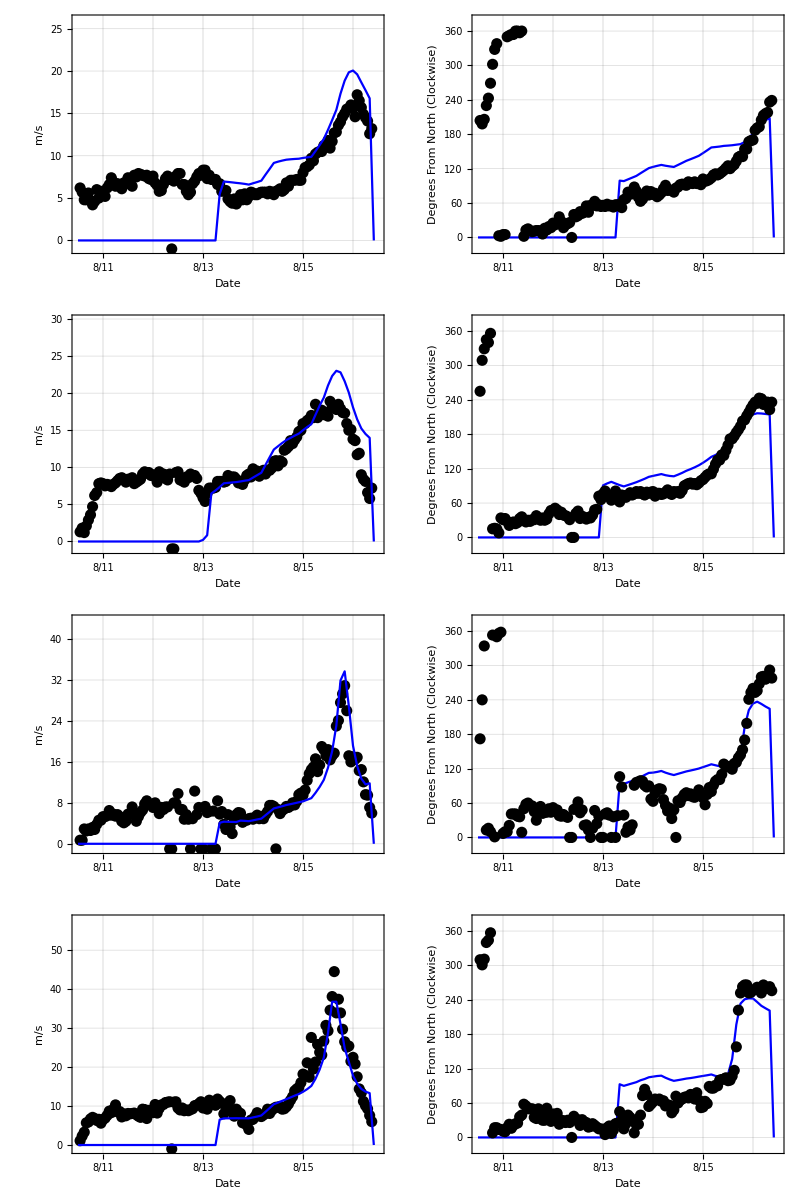

D:\Dropbox\floyd_noriverswindgrid.eps

```mathematica
Grid[plotlist]

Export[StringJoin[basedirectory,"windgrid.eps"],Grid[plotlist],ImageResolution->288]


Export[StringJoin[basedirectory,"windgrid.png"],Grid[plotlist]];
```

```mathematica
"D:\\Desktop\\Thesis Work\\irene\\windgrid.eps"
```

D:\Desktop\Thesis Work\irene\windgrid.eps

```mathematica
WSPDsimscatters[[1,Length[WSPDsimscatters[[1]]]]]
```

{3.14383×10^9,0.}

```mathematica
simstartdate
```

{1999,8,11,0,0,0}